# Extending the Dibaryon EFT

## Here we will work with amplitudes that are meromorphic in the complex p plane (and meromorphic in the complex E plane except for the scattering cut (the ip term)). The bubble factor reproduces the scattering cut, so the remaining poles shall be reproduced via the effective potential Veff, which is proportional to -1/pcotδ. We will start with the delta shell potential. The first step is to identify where the poles are (here we show both the poles of A and Veff).

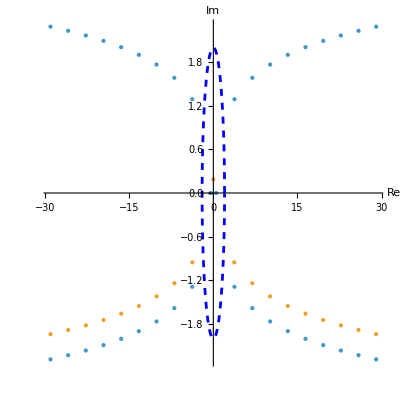

```mathematica
(*Parameters for the delta shell, following conventions in Gottfried*)
Rmax=10*Pi; (*All poles lie inside this radius in the ξ = p/Λ plane*)
g=1.2;
Rtest=2 ;

roots=NSolve[{SetPrecision[1-g*Sinc[z]*Cos[z],15]==0,-Rmax<Re[z]<Rmax,-Rmax<Im[z]<Rmax},z];
points=z/. roots; (*Will only find poles in lower right quadrant due to branch of inverse trig functions*)
allroots=DeleteDuplicates[Flatten[{#,-#,Conjugate[#],-Conjugate[#]}&/@points]]; (*Mirror to get all*)
plotpoles={Re[#],Im[#]}&/@allroots;

rootsamp=NSolve[{SetPrecision[1-g*Sinc[z]*Exp[I*z],15]==0,-Rmax<Re[z]<Rmax,-Rmax<Im[z]<Rmax},z];
pointsamp=z/. rootsamp;
allrootsamp=DeleteDuplicates[Flatten[{#,-Conjugate[#]}&/@pointsamp]];
plotamppoles={Re[#],Im[#]}&/@allrootsamp;

circle=Table[{Rtest Cos[θ],Rtest Sin[θ]},{θ,0,2 π,0.01}];
Show[ListPlot[{plotpoles,plotamppoles},AspectRatio->1,PlotStyle->{PointSize[Large]},AxesLabel->{"Re","Im"},PlotRange->All],ListLinePlot[circle,PlotStyle->{Blue,Dashed}]]
```

Poles in the amplitude map to pairs of poles in the effective potential (blue). See notes for how the residues are related from the symmetries of the S matrix.

```mathematica
energypoles=DeleteDuplicates[(#^2&)/@allroots] (*Poles in Veff as they appear in the energy plane*)
```

{0.26354787974184,12.47412455799-9.6989231187312 ⅈ,12.47412455799+9.6989231187312 ⅈ,45.88188175458-22.032515540648 ⅈ,45.88188175458+22.032515540648 ⅈ,99.367773156506-35.767292134346 ⅈ,99.367773156506+35.767292134346 ⅈ,172.76577842642-50.465547037996 ⅈ,172.76577842642+50.465547037996 ⅈ,266.0100400885-65.899889117351 ⅈ,266.0100400885+65.899889117351 ⅈ,379.06702484994-81.93021623565 ⅈ,379.06702484994+81.93021623565 ⅈ,511.91713691642-98.461371375912 ⅈ,511.91713691642+98.461371375912 ⅈ,664.54785587557-115.42445239631 ⅈ,664.54785587557+115.42445239631 ⅈ,836.95066097807-132.76724471189 ⅈ,836.95066097807+132.76724471189 ⅈ}

```mathematica
V[z_]:=Sinc[z]^2/(1-g*Sinc[z]*Cos[z]); (*The effective potential without the 4pi/M factor*)
Res[zr_]:=2*zr*(z-zr)*V[z]/.{z->zr+10^(-11)};
P[z_]:=2/g*Sin[z]^2/(Sinc[2*z]-Cos[2*z]); (*Residues of poles after using the symmetries*)
```

```mathematica
ROCs=Table[Abs[p],{p,allroots}] (*These are Abs[ξ] for the various poles, our series should converge up to the resonance that we don't include*)
```

{0.513369145685485,0.513369145685485,3.97505231263985,3.97505231263985,3.97505231263985,3.97505231263985,7.13426443095927,7.13426443095927,7.13426443095927,7.13426443095927,10.2766222656554,10.2766222656554,10.2766222656554,10.2766222656554,13.4158680324746,13.4158680324746,13.4158680324746,13.4158680324746,16.5544960581863,16.5544960581863,16.5544960581863,16.5544960581863,19.6931465808257,19.6931465808257,19.6931465808257,19.6931465808257,22.8319973362237,22.8319973362237,22.8319973362237,22.8319973362237,25.9710865485164,25.9710865485164,25.9710865485164,25.9710865485164,29.1104071962876,29.1104071962876,29.1104071962876,29.1104071962876}

```mathematica
ResidueTest=Table[P[p]-Res[p],{p,allroots}]
```

{1.74399×10^-6,-0.0000174106,1.76539×10^-7+3.15342×10^-6 ⅈ,-2.65739×10^-6-1.4167×10^-6 ⅈ,1.76539×10^-7-3.15342×10^-6 ⅈ,-2.65739×10^-6+1.4167×10^-6 ⅈ,-1.82796×10^-6+6.54015×10^-6 ⅈ,-2.42634×10^-7-7.64625×10^-6 ⅈ,-1.82796×10^-6-6.54015×10^-6 ⅈ,-2.42634×10^-7+7.64625×10^-6 ⅈ,-1.21882×10^-6-5.56868×10^-7 ⅈ,1.11033×10^-6-6.45474×10^-7 ⅈ,-1.21882×10^-6+5.56868×10^-7 ⅈ,1.11033×10^-6+6.45474×10^-7 ⅈ,1.64149×10^-6+1.77187×10^-6 ⅈ,-6.81647×10^-7+1.84015×10^-6 ⅈ,1.64149×10^-6-1.77187×10^-6 ⅈ,-6.81647×10^-7-1.84015×10^-6 ⅈ,-2.62499×10^-7+2.75336×10^-6 ⅈ,-3.73425×10^-7-1.8866×10^-6 ⅈ,-2.62499×10^-7-2.75336×10^-6 ⅈ,-3.73425×10^-7+1.8866×10^-6 ⅈ,2.89762×10^-6-1.08633×10^-6 ⅈ,-4.05681×10^-6-9.46199×10^-7 ⅈ,2.89762×10^-6+1.08633×10^-6 ⅈ,-4.05681×10^-6+9.46199×10^-7 ⅈ,-6.35489×10^-7+2.5818×10^-6 ⅈ,1.68145×10^-6+2.54149×10^-6 ⅈ,-6.35489×10^-7-2.5818×10^-6 ⅈ,1.68145×10^-6-2.54149×10^-6 ⅈ,-3.48574×10^-6+4.12193×10^-6 ⅈ,-5.80189×10^-6+4.15748×10^-6 ⅈ,-3.48574×10^-6-4.12193×10^-6 ⅈ,-5.80189×10^-6-4.15748×10^-6 ⅈ,-2.59543×10^-6-2.6837×10^-6 ⅈ,-1.53117×10^-7+6.54685×10^-6 ⅈ,-2.59543×10^-6+2.6837×10^-6 ⅈ,-1.53117×10^-7-6.54685×10^-6 ⅈ}

```mathematica
Poles[z_,points_]:=Sum[SetPrecision[P[Sqrt[points[[i]]]],15]/(z^2-points[[i]]),{i,1,Length[points]}];
Poles[ξ,Take[energypoles,5]] (*Construct the poles of the effective potential and sum them up, note the number in Take must be 1, 3, 5, etc for how many poles are included in the sum (1 bd state, then pairs of resonances in E plane)*)
```

(0.831489642838457-0.01173243686383 ⅈ)/((-45.88188175458-22.032515540648 ⅈ)+ξ^2)+(0.831489642838457+0.01173243686383 ⅈ)/((-45.88188175458+22.032515540648 ⅈ)+ξ^2)+(0.828697246696031-0.02141574705189 ⅈ)/((-12.47412455799-9.6989231187312 ⅈ)+ξ^2)+(0.828697246696031+0.02141574705189 ⅈ)/((-12.47412455799+9.6989231187312 ⅈ)+ξ^2)+1.27324357391004/(-0.26354787974184+ξ^2)

```mathematica
Residual[z_,n_]:=V[z]-Poles[z,Take[energypoles,n]]; (*Should be smooth and even in p!*)
```

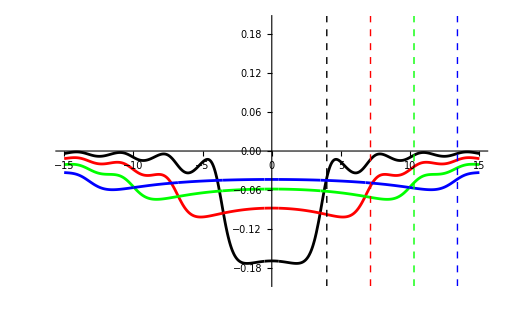

```mathematica
Bd=Plot[{Residual[z,1]},{z,-15,15},PlotStyle->Black];
Res1 = Plot[{Residual[z,3]},{z,-15,15},PlotStyle->Red];
Res2=Plot[{Residual[z,5]},{z,-15,15},PlotStyle->Green];
Res3=Plot[{Residual[z,7]},{z,-15,15},PlotStyle->Blue];

colors={Black,Red,Green,Blue};
vlines=Graphics[Table[{Directive[colors[[i]],Dashed],Line[{{ROCs[[4*i-1]],-1},{ROCs[[4*i-1]],1}}]},{i,Length[colors]}],Axes->True];
Show[{Bd,Res1,Res2,Res3},vlines,PlotRange->{{-15,15},{-0.2,0.2}}]
```

Above we see a plot of the residual function (Veff-poles) for successive numbers of poles. The vertical lines are the locations of the successive resonances above the ones that are included. In principle, they should characterize the true ROC of a Taylor series of the residual function. From the looks of it, good agreement should be achievable using only C0 and C2... (summing to all orders in the bubble sum)

```mathematica
(*xvals=Range[-8`15,8`15,0.1`15];
yvals=Table[SetPrecision[Residual[p,3],15],{p,xvals}];
Poly=Fit[Transpose[{xvals,yvals}],Table[x^i,{i,0,4,2}],x]*)
```

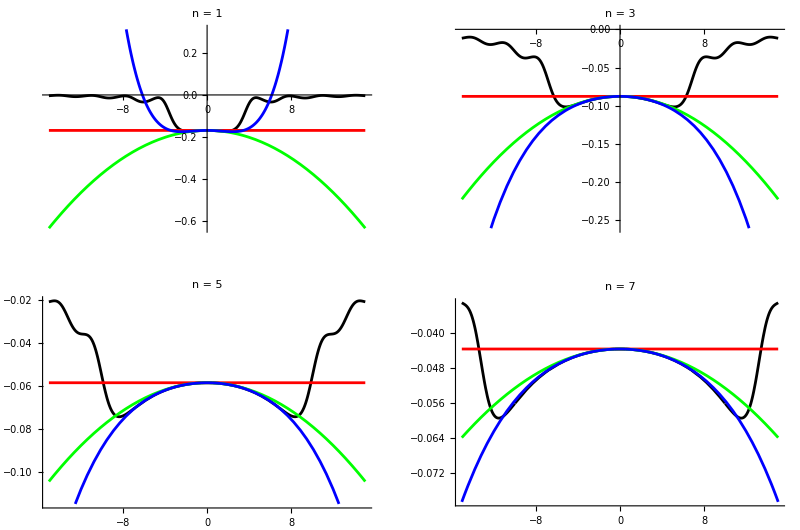

```mathematica
ApproxResidual[z_,n_,m_]:=Normal[Series[Residual[y,n],{y,0,m}]]/.{y->z} ;(*n characterizes the # of poles subtracted, m is order of the series*)
plots=Table[Plot[Evaluate@Flatten@{Residual[x,n],Table[ApproxResidual[x,n,i],{i,0,4,2}]},{x,-15,15},PlotStyle->{Black,Red,Green,Blue},PlotLabel->"n = "<>ToString[n]],{n,{1,3,5,7}} ];
GraphicsGrid[Partition[plots,2]]
```

We can reproduce the the residual function (up to around the next kink) using just the first 2-4 terms in the series. I have trouble getting Mathematica to go beyond fourth order. The derivatives it computes can be noisy, but this should be sufficient to see how well we can reproduce any observables (phase, cross section, etc)

```mathematica
Amplitude[z_]:=1/(-1/V[z]-I*z);
CrossSection[z_]:=Abs[Amplitude[z]]^2;
Vapprox[z_,n_,m_]:= Poles[z,Take[energypoles,n]]+ApproxResidual[z,n,m];
```

```mathematica
(*Computes the phase shift over some momentum range you specify, the wrapper unmods the phases to give a smooth curve*)
Phase[Veff_,z_]:=Re[Pi-ArcTan[-z*Veff[z]]] (*Force real part, but make sure has zero imaginary*)
momentumrange=Range[0.01,15,0.01];
PhaseShift[oldphases_]:=Module[{deltas,corrections},deltas=Differences[oldphases];
corrections=Accumulate[ Pi*Round[deltas/(Pi)]];
Prepend[oldphases[[2;;]]-corrections,oldphases[[1]]]]

ApproxPhase[n_,m_]:=Module[{F,l,yInt},F=Vapprox[q,n,m];l=Table[Pi-ArcTan[Re[-q*F]],{q,momentumrange}];yInt=Interpolation[Transpose[{momentumrange,PhaseShift[l]}]];yInt]

ExactPhase=Interpolation[Transpose[{momentumrange,PhaseShift[Table[Phase[V,z],{z,momentumrange}]]}]];
```

Below we construct the plots for the exact phase shift (always black) with the approximate phase shifts (including a given number of poles, and at several orders in the residual function expansion (red is LO, green is NLO, and Blue is NNLO).

```mathematica
p1=Plot[{ExactPhase[z],Evaluate[Table[ApproxPhase[1,i][z],{i,0,4,2}]]},{z,0.01,15},PlotStyle->{Black,Red,Green,Blue },PlotRange->All];
vline1=Graphics[{Gray,Dashed,Line[{{ROCs[[4*(1)-1]],-Pi},{ROCs[[4*(1)-1]],Pi}}]}];

p3=Plot[{ExactPhase[z],Evaluate[Table[ApproxPhase[3,i][z],{i,0,4,2}]]},{z,0.01,15},PlotStyle->{Black,Red,Green,Blue },PlotRange->All];
vline3=Graphics[{Gray,Dashed,Line[{{ROCs[[4*(2)-1]],-Pi},{ROCs[[4*(2)-1]],Pi}}]}];

p5=Plot[{ExactPhase[z],Evaluate[Table[ApproxPhase[5,i][z],{i,0,4,2}]]},{z,0.01,15},PlotStyle->{Black,Red,Green,Blue },PlotRange->All];
vline5=Graphics[{Gray,Dashed,Line[{{ROCs[[4*(3)-1]],-Pi},{ROCs[[4*(3)-1]],Pi}}]}];

p7=Plot[{ExactPhase[z],Evaluate[Table[ApproxPhase[7,i][z],{i,0,4,2}]]},{z,0.01,15},PlotStyle->{Black,Red,Green,Blue },PlotRange->All];
vline7=Graphics[{Gray,Dashed,Line[{{ROCs[[4*(4)-1]],-Pi},{ROCs[[4*(4)-1]],Pi}}]}];
```

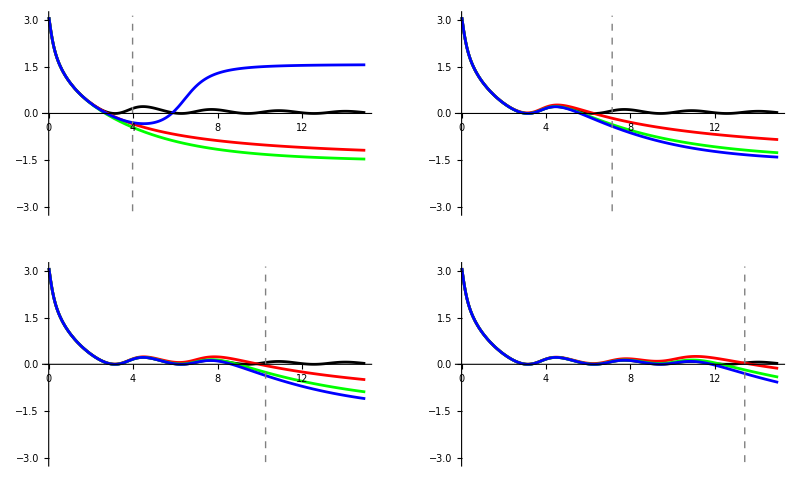

```mathematica
GraphicsGrid[{{Show[p1,vline1],Show[p3,vline3]},{Show[p5,vline5],Show[p7,vline7]}}]
```

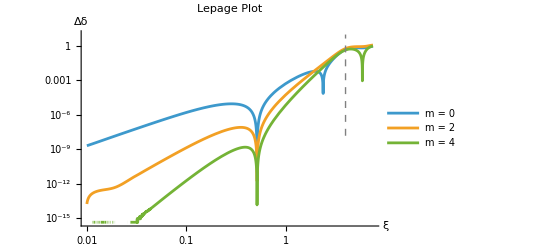

```mathematica
Lep1=LogLogPlot[Evaluate[Table[Abs[ExactPhase[z]-ApproxPhase[1,i][z]],{i,0,4,2}]],{z,0.01,7.5},PlotRange->All,PlotLegends->{"m = 0","m = 2","m = 4"},AxesLabel->{"ξ","Δδ"},PlotLabel->"Lepage Plot"];
Show[Lep1,Graphics[{Gray,Dashed,Line[{{Log[ROCs[[3]]],-18},{Log[ROCs[[3]]],Log[10]}}]}],PlotRange->All]
```

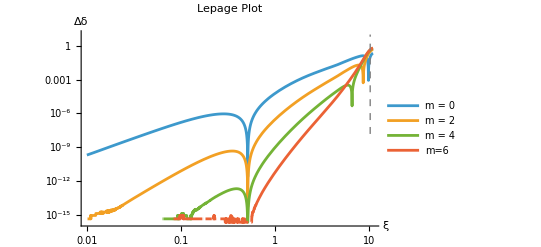

```mathematica
Lep5=LogLogPlot[Evaluate[Table[Abs[ExactPhase[z]-ApproxPhase[5,i][z]],{i,0,6,2}]],{z,0.01,11.0},PlotRange->All,PlotLegends->{"m = 0","m = 2","m = 4","m=6"},AxesLabel->{"ξ","Δδ"},PlotLabel->"Lepage Plot"];
Show[Lep5,Graphics[{Gray,Dashed,Line[{{Log[ROCs[[11]]],-18},{Log[ROCs[[11]]],Log[10]}}]}],PlotRange->All]
```